```mathematica
?ScalarMixedSpins
```

package for scalar and mixed ...
Designations(7): d t it p pp collectPP pTimes
Symbolic(9): expandSigma expandSigTimes HBasis basisH coordinates matrixTransform fullCoordinates(...) fullTransform(...) RemBasis
Traces(4): fastTr1 fastTr gramMatrix symGramMatrix
RhoGen(16): lastKP firstKP nextKP listKPs compoze swapToPerm generateGroup normolizeKP KPToExpr invariantKPsets KPsetsToExpr rhoGen invariantKPTsets listKPTs allKPs depsGen
Linerear algebra(8): RowReduceUpTo RowReduceUpToShow RowReduceInfo LinDeps ApplyLinDeps LinDependent LinIndependent DeleteReduced
ExplicitMatrices(13): getSi getSz getSp getSm getSx getSy KP scalar scalarSparse mixed mixedSparse explicit explicitSparse
Utilities(5):  FE foundQ firstFound printTo plusToList

```mathematica
?ScalarMixedSpins`*
```

ApplyLinDeps[matrix,deps,dependent] - return matrix with removed dependencies (apply to rows)
ApplyLinDeps[matrix,deps] - automatically find dependent rows and return {matrix without dependencies, dependent}

```mathematica
SolveShredinger2[H81_,basis81_]:=Module[
{vectors81,rems81,forbasis81,basis81GM,forbasis81GM,matrix81,deps81},
Print["вычисляем Hρ"];
Print[Timing[vectors81=Hbasis[H81,basis81]][[1]]//Round," сек"];
Print["вычисляем матрицу Грамма основного базиса"];
Print[Timing[basis81GM=symGramMatrix[basis81]][[1]]//Round," сек"];
Print["переполняющих векторов в основном базисе: ",Length[basis81]-MatrixRank[basis81GM]," из ",Length[basis81]];
Print["раскладываем Hρ по базису"];
Print[Timing[{matrix81,rems81}=matrixTransform[vectors81,basis81]][[1]]//Round," сек"];
Print["составляем вспомогательный базис и раскладываем по нему остатки"];
Print[Timing[{deps81,forbasis81}=RemBasis[rems81]][[1]]//Round," сек"];
Print["вычисляем матрицу Грамма вспомогательного базиса"];
Print[Timing[forbasis81GM=symGramMatrix[forbasis81/.it[a_,b_,c_]:>ⅈ t[a,b,c]]][[1]]//Round," сек"];
Print["переполняющих векторов во вспомогательном базисе: ",Length[forbasis81]-MatrixRank[forbasis81GM]," из ",Length[forbasis81]];
{vectors81,rems81,forbasis81,basis81GM,forbasis81GM,matrix81,deps81}
]
```

```mathematica
RestoreDeps[deps_,eigval_,eigvec_]:=Module[{
symbs=Unique[ConstantArray["x",Length[LinDependent[deps]]]],
vecs=ConstantArray[0,Length[deps[[1]]]]
},
vecs[[LinDependent[deps]]]=symbs;
vecs[[LinIndependent[deps]]]=eigvec;
(Remove@@symbs; #)&[vecs/.Solve[deps.vecs==0,symbs][[1]]]
]
```

```mathematica
SetDirectory["C:\\Users\\feelus\\Repos\\ScalarMixedSpins\\data"]
```

C:\Users\feelus\Repos\ScalarMixedSpins\data

## Ring 3 (0,2,0,0) (overflow_basis, basis, overflow_forbasis, forbasis)

```mathematica
group3=generateGroup[{{1->2,2->3,3->1}}]
```

{{1→1,2→2,3→3},{1→2,2→3,3→1},{1→3,2→1,3→2}}

```mathematica
basis3={1};
AppendTo[basis3,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,3,group3]];
basis3=basis3//Flatten
```

{1,d[1,2]+d[1,3]+d[2,3]}

```mathematica
H3=basis3[[2]]
```

d[1,2]+d[1,3]+d[2,3]

```mathematica
{vectors3,rems3,forbasis3,basisGM3,forbasisGM3,matrix3,deps3}=SolveShredinger2[H3,basis3];
```

вычисляем Hρ

0 сек

вычисляем матрицу Грамма основного базиса

0 сек

переполняющих векторов в основном базисе: 0 из 2

раскладяваем Hρ по базису

0 сек

составляем вспомогательный базис и раскладываем по нему остатки

0 сек

вычисляем матрицу Грамма вспомогательного базиса

0 сек

MatrixRank::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

переполняющих векторов во вспомогательном базисе: -MatrixRank[{}] из 0

```mathematica
vectors3
```

{d[1,2]+d[1,3]+d[2,3],9}

```mathematica
matrix3//MatrixForm
```

(0 | 9
1 | 0)

```mathematica
Expand[Transpose[matrix3].basis3]==vectors3
```

True

```mathematica
Eigensystem[matrix3]
```

{{-3,3},{{-3,1},{3,1}}}

```mathematica
Eigenvalues[explicit[1/2,3,H3]]
```

{-3,-3,-3,-3,3,3,3,3}

## Ring 4 (0,5,0,0)

```mathematica
group4=generateGroup[{{1->2,2->3,3->4,4->1}}]
```

{{1→1,2→2,3→3,4→4},{1→2,2→3,3→4,4→1},{1→3,2→4,3→1,4→2},{1→4,2→1,3→2,4→3}}

```mathematica
basis4={1};
AppendTo[basis4,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,4,group4]];
AppendTo[basis4,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,4,group4]];
basis4=basis4//Flatten
```

{1,d[1,2]+d[1,4]+d[2,3]+d[3,4],d[1,3]+d[2,4],d[1,3] d[2,4],d[1,4] d[2,3]+d[1,2] d[3,4]}

```mathematica
H4=basis4[[2]]
```

d[1,2]+d[1,4]+d[2,3]+d[3,4]

```mathematica
{vectors4,rems4,forbasis4,basisGM4,forbasisGM4,matrix4,deps4}=SolveShredinger2[H4,basis4];
```

вычисляем Hρ

0 сек

вычисляем матрицу Грамма основного базиса

0 сек

переполняющих векторов в основном базисе: 0 из 5

раскладяваем Hρ по базису

0 сек

составляем вспомогательный базис и раскладываем по нему остатки

0 сек

вычисляем матрицу Грамма вспомогательного базиса

0 сек

MatrixRank::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

переполняющих векторов во вспомогательном базисе: -MatrixRank[{}] из 0

```mathematica
Eigensystem[matrix4]
```

{{-8,-4,4,0,0},{{3,-2,1,-1,2},{-3,1,-1,-1,1},{15,5,5,1,1},{-1,0,0,1,0},{-2,0,1,0,0}}}

```mathematica
Eigenvalues[explicit[1/2,4,H4]]
```

{-8,-4,-4,-4,4,4,4,4,4,0,0,0,0,0,0,0}

## Ring 5 (0,6,0,0)

```mathematica
group5=generateGroup[{{1->2,2->3,3->4,4->5,5->1}}]
```

{{1→1,2→2,3→3,4→4,5→5},{1→2,2→3,3→4,4→5,5→1},{1→3,2→4,3→5,4→1,5→2},{1→4,2→5,3→1,4→2,5→3},{1→5,2→1,3→2,4→3,5→4}}

```mathematica
basis5={1};
AppendTo[basis5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,5,group5]];
AppendTo[basis5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,5,group5]];
basis5=basis5//Flatten
```

{1,d[1,2]+d[1,5]+d[2,3]+d[3,4]+d[4,5],d[1,3]+d[1,4]+d[2,4]+d[2,5]+d[3,5],d[1,3] d[2,4]+d[1,3] d[2,5]+d[1,4] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,5],d[1,4] d[2,3]+d[1,5] d[2,4]+d[2,5] d[3,4]+d[1,2] d[3,5]+d[1,3] d[4,5],d[1,5] d[2,3]+d[1,2] d[3,4]+d[1,5] d[3,4]+d[1,2] d[4,5]+d[2,3] d[4,5]}

```mathematica
H5=basis5[[2]]
```

d[1,2]+d[1,5]+d[2,3]+d[3,4]+d[4,5]

```mathematica
{vectors5,rems5,forbasis5,basisGM5,forbasisGM5,matrix5,deps5}=SolveShredinger2[H5,basis5];
```

вычисляем Hρ

0 сек

вычисляем матрицу Грамма основного базиса

0 сек

переполняющих векторов в основном базисе: 0 из 6

раскладяваем Hρ по базису

0 сек

составляем вспомогательный базис и раскладываем по нему остатки

0 сек

вычисляем матрицу Грамма вспомогательного базиса

0 сек

MatrixRank::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

переполняющих векторов во вспомогательном базисе: -MatrixRank[{}] из 0

```mathematica
Eigensystem[matrix5]
```

{{-3-2 √5,5,-3,-√5,√5,-3+2 √5},{{(15 (125+56 √5))/((5+2 √5) (56+25 √5)),-(11 (85+38 √5))/((5+2 √5) (56+25 √5)),-(-185-82 √5)/((5+2 √5) (56+25 √5)),-(30+13 √5)/((5+2 √5) (56+25 √5)),-(13+6 √5)/(56+25 √5),1},{15,5,5,1,1,1},{-5,1,1,1,-3,1},{-15/(1+√5),(√5)/(1+√5),-(√5)/(1+√5),-(-1+√5)/(1+√5),1/(1+√5),1},{15/(-1+√5),(√5)/(-1+√5),-(√5)/(-1+√5),-(1+√5)/(-1+√5),-1/(-1+√5),1},{-(15 (-125+56 √5))/((-5+2 √5) (-56+25 √5)),(11 (-85+38 √5))/((-5+2 √5) (-56+25 √5)),-(-185+82 √5)/((-5+2 √5) (-56+25 √5)),-(30-13 √5)/((-5+2 √5) (-56+25 √5)),-(-13+6 √5)/(-56+25 √5),1}}}

```mathematica
Eigenvalues[explicit[1/2,5,H5]]
```

{-3-2 √5,-3-2 √5,-3-2 √5,-3-2 √5,5,5,5,5,5,5,-3,-3,-√5,-√5,-√5,-√5,-√5,-√5,-√5,-√5,√5,√5,√5,√5,√5,√5,√5,√5,-3+2 √5,-3+2 √5,-3+2 √5,-3+2 √5}

## Ring 6 (0,18,2,8->14)

```mathematica
group6=generateGroup[{{1->2,2->3,3->4,4->5,5->6,6->1}}];
basis6={1};
AppendTo[basis6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,6,group6]];
AppendTo[basis6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,6,group6]];
AppendTo[basis6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,6,group6]];
basis6=basis6//Flatten;
Print[basis6//Length];
H6=basis6[[2]]
```

18

d[1,2]+d[1,6]+d[2,3]+d[3,4]+d[4,5]+d[5,6]

```mathematica
{vectors6,rems6,forbasis6,basisGM6,forbasisGM6,matrix6,deps6}=SolveShredinger2[H6,basis6];
```

вычисляем Hρ

1 сек

вычисляем матрицу Грамма основного базиса

1 сек

переполняющих векторов в основном базисе: 0 из 18

раскладяваем Hρ по базису

0 сек

составляем вспомогательный базис и раскладываем по нему остатки

0 сек

вычисляем матрицу Грамма вспомогательного базиса

1 сек

переполняющих векторов во вспомогательном базисе: 2 из 8

```mathematica
vectors6==Expand[Transpose[matrix6].basis6]+(rems6/.it[a_,b_,c_]:>ⅈ t[a,b,c])
```

True

```mathematica
rems6==Expand[Transpose[deps6].forbasis6]
```

True

```mathematica
{eigVals6,eigVecs6}=Eigensystem[matrix6];
```

```mathematica
eigVals6//Expand//Union
```

{-6,-4,-2,-1,0,2,4,6,-4-2 √5,-4+2 √5,-4-2 √13,-4+2 √13,-1-√17,-1+√17}

```mathematica
Eigenvalues[explicit[1/2,6,H6]]//Expand//Union
```

{-6,-4,-2,0,2,4,6,-4-2 √5,-4+2 √5,-4-2 √13,-4+2 √13,-1-√17,-1+√17}

```mathematica
For[i=1,i≤Length[eigVecs6],i++,If[Simplify[forbasisGM6.deps6.(eigVecs6[[i]])]==ConstantArray[0,Length[forbasis6]],Print[i,") ",eigVals6[[i]]//Expand]]];
```

1) -4-2 √13

2) -4-2 √5

3) -6

4) 6

5) -1-√17

9) 4

10) -4+2 √13

11) -1+√17

12) -2

13) -2

14) 2

17) -4+2 √5

18) 0

```mathematica
eigVals6//Expand//TableForm
```

-4-2 √13
-4-2 √5
-6
6
-1-√17
-4
-4
-4
4
-4+2 √13
-1+√17
-2
-2
2
-1
-1
-4+2 √5
0

```mathematica
LinIndependent[RowReduce[forbasisGM6.deps6]]//Length
```

14

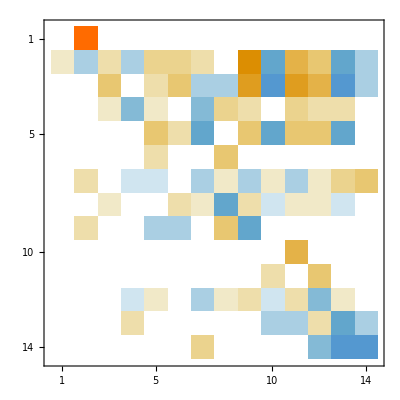

```mathematica
(realmatrix6=Transpose[ApplyLinDeps[Transpose[matrix6],forbasisGM6.deps6][[1]]][[LinIndependent[RowReduce[forbasisGM6.deps6]]]])//MatrixPlot
```

```mathematica
Eigenvalues[realmatrix6]//Expand//Union
```

{-6,-4,-2,0,2,4,6,-4-2 √5,-4+2 √5,-4-2 √13,-4+2 √13,-1-√17,-1+√17}

```mathematica
Eigenvalues[explicit[1/2,6,H6]]//Expand//Union
```

{-6,-4,-2,0,2,4,6,-4-2 √5,-4+2 √5,-4-2 √13,-4+2 √13,-1-√17,-1+√17}

## Ring 7 (0,34,12,39->21)

```mathematica
group7=generateGroup[{{1->2,2->3,3->4,4->5,5->6,6->7,7->1}}];
basis7={1};
AppendTo[basis7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,7,group7]];
AppendTo[basis7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,7,group7]];
AppendTo[basis7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,7,group7]];
basis7=basis7//Flatten;
Print[basis7//Length];
H7=basis7[[2]]
```

34

d[1,2]+d[1,7]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]

```mathematica
{vectors7,rems7,forbasis7,basisGM7,forbasisGM7,matrix7,deps7}=SolveShredinger2[H7,basis7];
```

вычисляем Hρ

4 сек

вычисляем матрицу Грамма основного базиса

12 сек

переполняющих векторов в основном базисе: 0 из 34

раскладяваем Hρ по базису

4 сек

составляем вспомогательный базис и раскладываем по нему остатки

3 сек

вычисляем матрицу Грамма вспомогательного базиса

24 сек

переполняющих векторов во вспомогательном базисе: 12 из 39

```mathematica
(realmatrix7=Transpose[ApplyLinDeps[Transpose[matrix7],forbasisGM7.deps7][[1]]][[LinIndependent[RowReduce[forbasisGM7.deps7]]]]);
```

```mathematica
realmatrix7//Length
```

21

```mathematica
Eigenvalues[realmatrix7]//Expand//Union
```

{-5,-3,3,7,Root[7+7 #1-7 #1^2+#1^3&,1],Root[7+7 #1-7 #1^2+#1^3&,2],Root[7+7 #1-7 #1^2+#1^3&,3],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,1],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,2],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,3],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,4],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,5],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,6],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,1],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,2],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,3],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,4],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,5],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,6]}

```mathematica
Eigenvalues[explicit[1/2,7,H7]]//Expand//Union
```

{-5,-3,3,7,Root[7+7 #1-7 #1^2+#1^3&,1],Root[7+7 #1-7 #1^2+#1^3&,2],Root[7+7 #1-7 #1^2+#1^3&,3],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,1],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,2],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,3],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,4],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,5],Root[769+1126 #1+159 #1^2-172 #1^3-33 #1^4+6 #1^5+#1^6&,6],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,1],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,2],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,3],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,4],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,5],Root[1261+1066 #1-1473 #1^2-412 #1^3+51 #1^4+18 #1^5+#1^6&,6]}

## Ring 8 (3,108->105,73,157->47)

```mathematica
Root[-64+16 #1+16 #1^2+#1^3&,1]//N
```

-14.6044

```mathematica
group8=generateGroup[{{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1}}]
```

{{1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8},{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→1},{1→3,2→4,3→5,4→6,5→7,6→8,7→1,8→2},{1→4,2→5,3→6,4→7,5→8,6→1,7→2,8→3},{1→5,2→6,3→7,4→8,5→1,6→2,7→3,8→4},{1→6,2→7,3→8,4→1,5→2,6→3,7→4,8→5},{1→7,2→8,3→1,4→2,5→3,6→4,7→5,8→6},{1→8,2→1,3→2,4→3,5→4,6→5,7→6,8→7}}

```mathematica
basis8={1};
AppendTo[basis8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,group8]];
AppendTo[basis8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,8,group8]];
AppendTo[basis8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,8,group8]];
AppendTo[basis8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[4,8,group8]];
basis8=basis8//Flatten
```

{1,d[1,2]+d[1,8]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8],104,d[1,8] d[2,7] d[3,4] d[5,6]+d[1,8] d[2,3] d[4,7] d[5,6]+d[1,8] d[2,5] d[3,4] d[6,7]+d[1,2] d[3,8] d[4,5] d[6,7]+d[1,2] d[3,4] d[5,8] d[6,7]+d[1,6] d[2,3] d[4,5] d[7,8]+d[1,2] d[3,6] d[4,5] d[7,8]+d[1,4] d[2,3] d[5,6] d[7,8],d[1,8] d[2,3] d[4,5] d[6,7]+d[1,2] d[3,4] d[5,6] d[7,8]}
 |  |  |  |

```mathematica
H8=basis8[[2]]
```

d[1,2]+d[1,8]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8]

```mathematica
{vectors8,rems8,forbasis8,basisGM8,forbasisGM8,matrix8,deps8}=SolveShredinger2[H8,basis8];
```

вычисляем Hρ

20 сек

вычисляем матрицу Грамма основного базиса

167 сек

переполняющих векторов в основном базисе: 3 из 108

раскладяваем Hρ по базису

118 сек

составляем вспомогательный базис и раскладываем по нему остатки

76 сек

вычисляем матрицу Грамма вспомогательного базиса

819 сек

переполняющих векторов во вспомогательном базисе: 73 из 157

```mathematica
Put[{vectors8,rems8,forbasis8,basisGM8,forbasisGM8,matrix8,deps8},"Matrices8.m"]
```

```mathematica
{vectors8,rems8,forbasis8,basisGM8,forbasisGM8,matrix8,deps8}=Get["Matrices8.m"];
```

```mathematica
deps8a=basisGM8//LinDeps;
independent8=LinIndependent[deps8a//RowReduce];
matrix8r=ApplyLinDeps[matrix8,deps8a][[1]][[;;,independent8]];
deps8r=deps8[[;;,independent8]];
(clearMatrix8=Transpose[ApplyLinDeps[Transpose[matrix8r],forbasisGM8.deps8r][[1]]][[LinIndependent[RowReduce[forbasisGM8.deps8r]]]]);
```

```mathematica
Eigenvalues[matrix8r]//TableForm
```

Root[-64+16 #1+16 #1^2+#1^3&,1]
Root[-320-32 #1+12 #1^2+#1^3&,1]
Root[-192-48 #1+8 #1^2+#1^3&,1]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,1]
Root[40+68 #1+16 #1^2+#1^3&,1]
Root[-8+28 #1+12 #1^2+#1^3&,1]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,2]
8
Root[-32+8 #1^2+#1^3&,1]
Root[-64-32 #1+4 #1^2+#1^3&,1]
Root[-24+4 #1+8 #1^2+#1^3&,1]
2 (-2-√2)
2 (2+√2)
Root[40+68 #1+16 #1^2+#1^3&,2]
2 (-1-√5)
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,1]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,1]
Root[-32-32 #1+#1^3&,3]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,2]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,2]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,3]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,3]
Root[-192-48 #1+8 #1^2+#1^3&,3]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,8]
Root[-320-32 #1+12 #1^2+#1^3&,3]
Root[-32-32 #1+#1^3&,1]
Root[-64-32 #1+4 #1^2+#1^3&,3]
Root[4+16 #1+8 #1^2+#1^3&,1]
Root[4+16 #1+8 #1^2+#1^3&,1]
Root[-320-32 #1+12 #1^2+#1^3&,2]
-2 √(3+√5)
2 √(3+√5)
Root[-8-4 #1+4 #1^2+#1^3&,1]
-4
4
4
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,4]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,4]
Root[-8+28 #1+12 #1^2+#1^3&,2]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,7]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,3]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,12]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,12]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,5]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,5]
Root[4-8 #1+#1^3&,1]
Root[4-8 #1+#1^3&,1]
Root[-192-48 #1+8 #1^2+#1^3&,2]
Root[-64+16 #1+16 #1^2+#1^3&,2]
Root[4+16 #1+8 #1^2+#1^3&,2]
Root[4+16 #1+8 #1^2+#1^3&,2]
Root[4-8 #1+#1^3&,3]
Root[4-8 #1+#1^3&,3]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,4]
Root[-24+4 #1+8 #1^2+#1^3&,2]
2 (-1+√5)
Root[-32+8 #1^2+#1^3&,2]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,6]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,6]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,5]
-2
-2
-2
-2
2
2
Root[-32+8 #1^2+#1^3&,3]
Root[-64-32 #1+4 #1^2+#1^3&,2]
-2 √(3-√5)
2 √(3-√5)
Root[-8-4 #1+4 #1^2+#1^3&,3]
Root[-64+16 #1+16 #1^2+#1^3&,3]
-√2
-√2
√2
√2
Root[-24+4 #1+8 #1^2+#1^3&,3]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,7]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,7]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,8]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,8]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,11]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,11]
2 (-2+√2)
2 (2-√2)
Root[-8-4 #1+4 #1^2+#1^3&,2]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,6]
Root[-32-32 #1+#1^3&,2]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,10]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,10]
Root[40+68 #1+16 #1^2+#1^3&,3]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,9]
Root[15872-20224 #1-48928 #1^2+27904 #1^3+61680 #1^4+5312 #1^5-24136 #1^6-11808 #1^7-956 #1^8+672 #1^9+210 #1^10+24 #1^11+#1^12&,9]
Root[4-8 #1+#1^3&,2]
Root[4-8 #1+#1^3&,2]
Root[4+16 #1+8 #1^2+#1^3&,3]
Root[4+16 #1+8 #1^2+#1^3&,3]
Root[-8+28 #1+12 #1^2+#1^3&,3]
0
0
0
0
0
0
0

```mathematica
Eigenvalues[clearMatrix8]//TableForm
```

Root[-64+16 #1+16 #1^2+#1^3&,1]
Root[-320-32 #1+12 #1^2+#1^3&,1]
Root[-192-48 #1+8 #1^2+#1^3&,1]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,1]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,2]
8
Root[-32+8 #1^2+#1^3&,1]
Root[-64-32 #1+4 #1^2+#1^3&,1]
2 (-2-√2)
2 (2+√2)
2 (-1-√5)
Root[-32-32 #1+#1^3&,3]
Root[-192-48 #1+8 #1^2+#1^3&,3]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,8]
Root[-320-32 #1+12 #1^2+#1^3&,3]
Root[-32-32 #1+#1^3&,1]
Root[-64-32 #1+4 #1^2+#1^3&,3]
Root[-320-32 #1+12 #1^2+#1^3&,2]
-2 √(3+√5)
2 √(3+√5)
-4
4
4
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,7]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,3]
Root[-192-48 #1+8 #1^2+#1^3&,2]
Root[-64+16 #1+16 #1^2+#1^3&,2]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,4]
2 (-1+√5)
Root[-32+8 #1^2+#1^3&,2]
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,5]
Root[-32+8 #1^2+#1^3&,3]
Root[-64-32 #1+4 #1^2+#1^3&,2]
-2 √(3-√5)
2 √(3-√5)
Root[-64+16 #1+16 #1^2+#1^3&,3]
2 (-2+√2)
2 (2-√2)
Root[-32768+24576 #1^2+7168 #1^3-1984 #1^4-768 #1^5+8 #1^6+16 #1^7+#1^8&,6]
Root[-32-32 #1+#1^3&,2]
0
0
0
0
0
0
0

```mathematica
Timing[{eigvals8c,eigvecs8c}=Eigensystem[clearMatrix8]][[1]]//Round
```

Eigensystem::eivn: Incorrect number 3 of eigenvectors for eigenvalue -2\ (-2 + √2) with multiplicity 1.

Eigensystem::eivn: Incorrect number 7 of eigenvectors for eigenvalue 2\ (-2 + √2) with multiplicity 1.

Eigensystem::eivn: Incorrect number 8 of eigenvectors for eigenvalue 2\ (-1 + √5) with multiplicity 1.

General::stop: Further output of Eigensystem :: eivn will be suppressed during this calculation.

```mathematica
NullSpace[clearMatrix8+2 (-2+√2)IdentityMatrix[clearMatrix8//Length]]//Length
```

$Aborted

```mathematica
m=clearMatrix8+2 (-2+√2)IdentityMatrix[clearMatrix8//Length];
```

```mathematica
r1=RowSimplify[m,30];
```

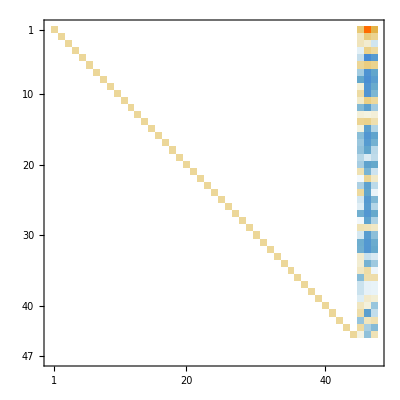

```mathematica
r1//MatrixPlot
```

```mathematica
NullSpace[r]
```

{{-105 (4+3 √2),-35/2 (1+√2),0,-7/2 (3+2 √2),14 (4+3 √2),-14-21/(√2),7/4 (14+9 √2),7/2 (11+7 √2),1/2 (37+27 √2),5 (4+3 √2),1/4 (-46-31 √2),6+9/(√2),0,-3/2 (3+2 √2),7/4 (4+3 √2),7/4 (10+7 √2),1/4 (52+37 √2),3/2 (3+2 √2),0,6+9/(√2),3/2 (3+2 √2),-3/2 (3+2 √2),2 (3+2 √2),2 (3+2 √2),5 (3+2 √2),7/2 (3+2 √2),1/2 (33+23 √2),2 (3+2 √2),1/4 (-4-3 √2),1/4 (38+25 √2),11/2 (3+2 √2),1/2 (33+23 √2),1+√2,4+3 √2,1/8 (-18-13 √2),1/8 (-30-19 √2),0,0,1/4 (-4-3 √2),1/8 (6+√2),2 (4+3 √2),1/2 (-5-3 √2),1/8 (26+17 √2),1/8 (14+13 √2),-1-√2,1/8 (26+19 √2),1}}

```mathematica
eigvecs8s=ConstantArray[0,{Length[eigvecs8c],Length[eigvecs8c[[1]]]}];
Timing[Monitor[
For[i=1,i≤Length[eigvecs8c],i++,
For[j=1,j<=Length[eigvecs8c[[1]]],j++,
eigvecs8s[[i,j]]=eigvecs8c[[i,j]]//Simplify;
]
],
ProgressIndicator[(i*Length[eigvecs8c[[1]]]+j)/Length[eigvecs8c]/Length[eigvecs8c[[1]]]]
]][[1]]//Round
```

951

```mathematica
Put[{eigvals8c,eigvecs8s},"Eigensystem8c.m"]
```

```mathematica
For[i=1,i≤Length[eigvals8c],i++,
vecs=RestoreDeps[RowReduce[forbasisGM8.deps8r],eigvals8c[[i]],eigvecs8s[[i]]];
(*d=matrix91.N[vecs91]-N[eigvals91[[i]]]N[ vecs91];
Print[d.d]*)
Print[i," ",N[matrix8r.vecs]-N[eigvals8c[[i]] vecs]]
]
```

## Ring 9 (14,294->280,374,639->)

```mathematica
group9=generateGroup[{{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->1}}]
```

{{1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9},{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→1},{1→3,2→4,3→5,4→6,5→7,6→8,7→9,8→1,9→2},{1→4,2→5,3→6,4→7,5→8,6→9,7→1,8→2,9→3},{1→5,2→6,3→7,4→8,5→9,6→1,7→2,8→3,9→4},{1→6,2→7,3→8,4→9,5→1,6→2,7→3,8→4,9→5},{1→7,2→8,3→9,4→1,5→2,6→3,7→4,8→5,9→6},{1→8,2→9,3→1,4→2,5→3,6→4,7→5,8→6,9→7},{1→9,2→1,3→2,4→3,5→4,6→5,7→6,8→7,9→8}}

```mathematica
basis9={1};
AppendTo[basis9,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,9,group9]];
AppendTo[basis9,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,9,group9]];
AppendTo[basis9,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,9,group9]];
AppendTo[basis9,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[4,9,group9]];
basis9=basis9//Flatten
```

{1,d[1,2]+d[1,9]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8]+d[8,9],291,d[1,9] d[2,3] d[4,5] d[6,7]+d[1,9] d[2,3] d[4,5] d[7,8]+d[1,9] d[2,3] d[5,6] d[7,8]+d[1,2] d[3,4] d[5,6] d[7,8]+d[1,9] d[3,4] d[5,6] d[7,8]+d[1,2] d[3,4] d[5,6] d[8,9]+d[1,2] d[3,4] d[6,7] d[8,9]+d[1,2] d[4,5] d[6,7] d[8,9]+d[2,3] d[4,5] d[6,7] d[8,9]}
 |  |  |  |

```mathematica
H9=basis9[[2]]
```

d[1,2]+d[1,9]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8]+d[8,9]

```mathematica
{vectors9,rems9,forbasis9,basisGM9,forbasisGM9,matrix9,deps9}=SolveShredinger2[H9,basis9];
```

вычисляем Hρ

104 сек

вычисляем матрицу Грамма основного базиса

3154 сек

переполняющих векторов в основном базисе: 14 из 294

раскладяваем Hρ по базису

3672 сек

составляем вспомогательный базис и раскладываем по нему остатки

1362 сек

вычисляем матрицу Грамма вспомогательного базиса

32062 сек

переполняющих векторов во вспомогательном базисе: 374 из 639

```mathematica
deps9a=basisGM9//LinDeps;
```

```mathematica
matrix9r=Transpose[ApplyLinDeps[Transpose[ApplyLinDeps[matrix9,deps9a][[1]]],deps9a][[1]]];
```

```mathematica
{Length[matrix9r],Length[matrix9r[[1]]]}
```

```mathematica
deps9r=Transpose[ApplyLinDeps[Transpose[deps9],deps9a][[1]]];
```

```mathematica
(realmatrix9=Transpose[ApplyLinDeps[Transpose[matrix9r],forbasisGM9.deps9r][[1]]][[LinIndependent[RowReduce[forbasisGM9.deps9r]]]]);
```

```mathematica
realmatrix9//Length
```

```mathematica
Eigenvalues[realmatrix9]//Expand//Union
```

```mathematica
Timing[control9=Eigenvalues[explicit[1/2,9,H9]]];
```

$Aborted

```mathematica
Return
```

## Mathematica bugs

```mathematica
clearMatrix8={{0,24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-2,2,-2,5,5,0,17,-9,-1,-3,-3,8,53/2,-39/2,-1,-1/2,-39/2,26,11,2,6,-23/2,-25/2,-20,-3,-29/2,-7,9/2,1/2,22,37/2,19,-34,-89/2,-8,155/2,-4,-31,22,31/2,-2,-7,17,-23/2,-79/2,-5/2},{0,0,4,0,4,0,16,0,-12,8,8,-4,-16,8,-12,-20,16,20,-12,12,-4,-20,-4,-16,-12,-20,-42,-16,52,16,4,66,52,-24,52,-24,72,-72,-36,32,-32,20,-36,0,-24,16,-8},{0,0,1,-3,1,0,3,-1,-7,6,2,-1,-2,19/2,-29/2,-3,9/2,13/2,-6,6,-1,-1,-1/2,-11/2,-8,-5,-19/2,2,37/2,11/2,6,37/2,23,-12,11/2,-3,59/2,-15,-19,9,-13/2,4,-9,-2,-7/2,-9/2,-7/2},{0,0,0,0,8,0,0,0,-16,8,8,0,0,-4,12,-32,12,-12,8,-8,0,0,-12,-12,-16,-8,0,0,4,20,16,32,40,-16,12,-24,0,-36,40,64,-52,0,-16,40,-28,20,-12},{0,0,0,0,0,4,4,0,4,-4,-4,-4,4,16,-16,20,-8,0,4,8,0,4,4,4,0,8,-4,4,-8,-16,0,-16,-16,0,-20,16,26,22,-36,-36,32,-4,12,-20,20,-24,4},{0,0,1,-1,-1,2,-1,3,5,-6,-1,-1,3,-7/2,9/2,12,-21/2,25/2,2,6,1,-9,13/2,7/2,11,4,1/2,-11,11/2,-17/2,-11,-17/2,-19,4,33/2,4,-9/2,12,-22,-15,21/2,11,-6,-9,-19/2,-9/2,17/2},{0,2,0,0,-2,-2,4,-4,2,-2,2,2,-4,-9,15,2,-3,15,-8,-2,0,-8,7,9,14,-2,1,-6,-1,-1,-8,-1,-14,12,17,8,-21,-2,6,4,-15,4,2,6,-13,11,5},{0,0,0,0,1,0,0,0,-4,2,-2,0,4,9,-9,-2,3,-11,6,-2,2,10,-5,-3,-10,2,1,8,-9,1,10,-1,6,-6,-25,-2,13,2,6,0,11,-6,8,4,13,-13,-3},{0,0,0,0,0,0,0,0,0,4,-8,0,8,26,-22,16,-6,-14,8,4,0,16,-2,2,-12,16,8,16,-22,-14,12,-28,0,-8,-46,16,18,40,-24,-24,26,-16,20,-8,30,-30,-2},{0,0,0,0,0,0,0,0,0,0,-2,2,4,9,-5,8,-5,-3,4,2,0,4,1,1,-2,6,3,4,-7,-7,2,-11,-6,0,-13,6,5,16,-10,-10,9,-4,6,-2,7,-11,1},{0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,2,0,0,0,0,2,-2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,1,-1,1,1,-1,1,2,1,0,-1,1,2,1,0,-1,-1,1,0,-1,1,-2,-1,3,3,2,-1,-3,1,-1,1,-1,0,-4,0,1},{0,0,0,0,1,0,0,0,-4,2,4,0,-2,-6,7,-11,7,-1,0,-3,1,-1,-3,-1,-2,-5,-2,0,1,7,2,11,11,-5,5,-3,-3,-14,13,21,-15,0,-5,10,-11,10,-2},{0,0,0,0,1,0,0,0,-1,1,1,0,0,1/2,-3/2,-3,3/2,-5/2,2,-1,-1,1,-3/2,-3/2,-2,0,-1/2,1,1/2,5/2,2,7/2,5,-2,3/2,-2,5/2,-5,4,6,-11/2,-1,-1,3,-3/2,5/2,-5/2},{0,0,0,0,0,0,2,0,0,0,0,0,-4,-1,3,-4,3,7,-4,0,-2,-4,1,-1,0,-4,-5,-2,5,1,-2,7,4,4,7,-6,3,-8,0,2,-5,2,-4,0,-1,5,-1},{0,0,0,0,0,1,0,0,2,-2,-1,1,0,1,1,6,-5,4,0,2,-1,-3,1,2,4,1,1,-2,1,-4,-4,-4,-7,4,5,2,-2,5,-7,-10,5,2,0,-6,2,-1,2},{0,0,0,1,0,0,1,0,2,-2,0,0,-1,-3,6,4,-4,2,1,-1,-1,-3,3,3,2,0,1,-3,-3,-3,-4,-3,-11,5,8,2,-7,1,1,-1,-3,4,2,3,-4,6,3},{0,0,0,0,0,1,0,0,2,-2,-2,-1,3,13/2,-11/2,8,-5/2,-1/2,1,1,0,4,3/2,5/2,-1,3,3/2,5,-15/2,-13/2,1,-21/2,-8,2,-27/2,6,9/2,13,-9,-15,27/2,-3,8,-6,21/2,-23/2,3/2},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,-2,4,-2,2,0,4,0,-4,2,-2,0,0,-4,-4,10,-2,0,4,-4,0,2,0,8,-2,-8,-4,2,4,0,0,-2,-6,2},{0,0,0,0,0,0,2,0,0,0,1,0,-4,-5/2,5/2,-2,-1/2,7/2,-3,2,-4,-6,-1/2,-5/2,2,0,-7/2,-6,21/2,5/2,-4,15/2,3,3,37/2,-6,1/2,-7,-2,2,-13/2,4,-8,-1,-9/2,25/2,1/2},{0,0,0,0,1,0,0,0,-3,1,2,0,-1,1/2,1/2,-4,3/2,-5/2,1,-1,0,-1,-1/2,-3/2,-4,-2,-3/2,1,5/2,7/2,4,11/2,5,-2,-7/2,-2,9/2,-5,4,8,-11/2,-1,0,6,-5/2,-1/2,-3/2},{0,0,0,0,0,1,0,0,3,-3,-1,-1,3,-1,1,9,-9,4,1,3,0,-2,2,2,5,6,4,-2,-1,-6,-5,-11,-13,5,2,4,-6,15,-10,-13,8,2,1,-5,1,-5,4},{0,0,0,-1,1,0,1,0,-4,2,1,0,1,1/2,-7/2,-6,7/2,3/2,-4,-1,0,-1,-3/2,-7/2,-4,-6,-5/2,-1,15/2,11/2,4,25/2,10,-4,9/2,-6,13/2,-15,4,16,-23/2,4,-6,9,-21/2,5/2,-1/2},{0,0,0,0,0,0,0,3,-2,0,0,0,-2,-5,7,-6,3,-5,2,0,0,-2,-3,-3,-4,2,-2,-2,3,3,-2,4,8,-2,7,-6,-3,-2,4,6,-2,-1,-8,0,-1,13,0},{0,0,0,0,0,0,2,0,1,-1,0,0,-1,1/2,-3/2,0,-1/2,3/2,-3,1,1,-1,3/2,1/2,2,-4,-7/2,-1,1/2,-1/2,0,3/2,-3,2,5/2,0,11/2,-4,-3,-5,5/2,1,0,-3,3/2,-1/2,1/2},{0,0,0,0,0,0,2,0,0,0,0,0,-4,-2,0,-4,6,0,-4,0,-2,-2,-2,-4,-2,-2,-8,2,10,2,0,10,10,0,6,-8,6,-12,4,2,-4,0,-4,-2,4,6,-4},{0,0,0,1,0,0,1,0,-1,-1,2,0,-3,-9,10,-6,2,4,-1,-2,0,-6,-1,-1,3,-5,-2,-9,7,5,-5,13,2,2,16,-8,-6,-16,11,13,-12,6,-8,6,-13,11,0},{0,0,0,0,1,0,0,0,-3,1,2,0,1,-7/2,5/2,-6,3/2,-1/2,0,-2,1,0,-3/2,-1/2,-1,-4,3/2,-2,1/2,11/2,1,15/2,5,-3,11/2,-3,-5/2,-10,9,15,-23/2,2,-4,9,-21/2,11/2,-1/2},{0,0,0,0,0,0,2,0,2,-2,-2,-2,0,1,-1,2,-1,3,0,2,0,-2,3,1,2,0,-5,-2,1,-5,0,-1,-6,4,5,0,5,-2,-6,-10,5,2,0,-6,3,-1,1},{0,0,0,0,0,0,0,3,0,0,-1,0,0,-1/2,-3/2,-2,-5/2,-9/2,3,0,0,2,-5/2,-9/2,-4,2,3/2,-2,1/2,9/2,-2,1/2,5,-3,-19/2,-6,13/2,5,0,4,5/2,-3,-2,3,3/2,-7/2,-5/2},{0,0,0,0,0,0,2,0,0,0,0,0,-4,-2,0,-4,6,0,-4,0,-2,-2,-2,-4,-2,-2,-8,2,10,2,0,10,10,0,6,-8,6,-12,4,2,-4,0,-4,-2,4,6,-4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,-1,0,0,-3,2,-1,-1,0,0,0,-1,-1,-1,-2,-1,0,2,3,1,4,3,-2,-3,-2,4,-2,1,5,-3,0,-1,1,-2,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,4,1,1,1,0,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,1,5/2,-7/2,2,-1/2,-3/2,1,1,0,1,-1/2,-1/2,-1,2,-1/2,1,1/2,-3/2,1,-3/2,-1,0,-3/2,0,5/2,1,-3,-4,11/2,-1,0,-3,11/2,-7/2,-1/2},{0,0,0,0,0,0,0,0,0,0,-1,0,1,5/2,-7/2,2,-1/2,-3/2,1,1,0,1,-1/2,-1/2,-1,2,-1/2,1,1/2,-3/2,1,-3/2,-1,0,-3/2,0,5/2,1,-3,-4,11/2,-1,0,-3,11/2,-7/2,-1/2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,4,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,-7/2,7/2,-2,1/2,5/2,-1,0,0,-2,1/2,1/2,2,-2,-1/2,-2,3/2,3/2,-2,5/2,-7,-1,15/2,-6,-3/2,-2,1,2,-7/2,4,-4,-1,-11/2,11/2,1/2},{0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,-4,2,0,0,-4,0,0},{0,0,0,0,0,0,0,0,0,0,-2,0,2,7,-7,4,-1,-5,4,0,0,6,-1,1,-4,4,1,6,-7,-3,4,-7,2,-2,-17,8,7,8,-4,-8,13,-8,6,-4,11,-13,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,-3,2,-1,0,2,0,1,1,-1,0,0,2,-1,-1,-2,2,0,-2,2,-1,-1,6,-5,-3,-5,0,3,-2,2,-5,2,-2,3,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,2,-1,-1,0,0,0,0,1,1,-2,0,1,0,-1,-1,2,-1,2,2,-5,6,0,1,-1,-4,-1,0,4,0,-3,-3,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,2,-1,-1,0,0,-2,0,1,1,0,2,1,2,-1,-1,0,-3,-8,0,-1,2,-1,6,-2,-4,-1,-2,2,-4,-1,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,2,0,-4,0,-2,-2,0,-1,0,-2,0,1,0,-8,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,-8,0,0,-4,0,0,0,0,-4,-4,0,-4,0,-8,-8}};
```

```mathematica
Off[General::eivn]
```

```mathematica
Timing[{eigvals8c,eigvecs8c}=Eigensystem[clearMatrix8]][[1]]//Round
```

```mathematica
m=clearMatrix8+2 (-2+√2)IdentityMatrix[clearMatrix8//Length];
```

```mathematica
r1=RowReduce[m]//Simplify;
```

```mathematica
r=RowSimplify[m,10];
```

```mathematica
deps8a={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,-3,2,-2,2,-1,-1,1,1,1,-1,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,-8,6,-4,8,-3,-5,2,2,2,-1,0,0,3,-1,-2,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,-3,2,-2,3,-1,-2,1,1,1,0,-1,0,1,-1,0,0,1}};
```

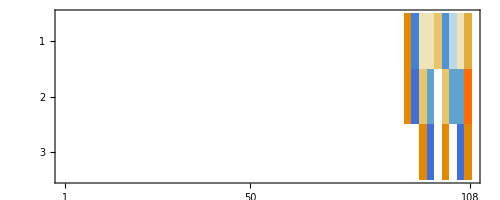

```mathematica
deps8a//RowReduce//MatrixPlot
```